```mathematica
M:=1
rplus[l_]:=(l^2/(2M))×(1+Sqrt[1-(12 M^2/l^2)])
rminus[l_]:=(l^2/(2M))×(1-Sqrt[1-(12 M^2/l^2)])
plotCallouts:={
Inset[Framed[Style["Stable Orbit",10],Background->LightYellow],{0.75,6.75}],
Inset[Framed[Style["Unstable Orbit",10],Background->LightYellow],{0.75,3.75}],
Inset[Framed[Style["L/m =(12)^(1/2) M",10],Background->LightYellow],{(Sqrt[12]×M-0.55),12}]
}
```

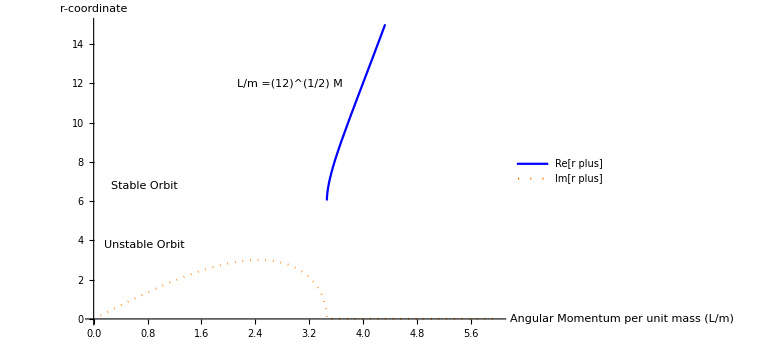

```mathematica
Plot[
{
rplus[l],Im[rplus[l]]
},
{
l,0,6M
},
AxesLabel->{
"Angular Momentum per unit mass (L/m)","r-coordinate"
},
PlotLegends->{
"Re[r plus]","Im[r plus]"
},
 ImageSize->Large,
Exclusions->None,
GridLines->{
{
{Sqrt[12]×M, Dashed}
},
{
{3M, {Pink, Dashed}}, {6M, {Red, Dashed}}
}
},
PlotStyle->{
{Blue,Thick},{Orange,Dotted}
},
PlotRange->{
{0,6M},{0,15M}
},
Epilog->plotCallouts
]
```

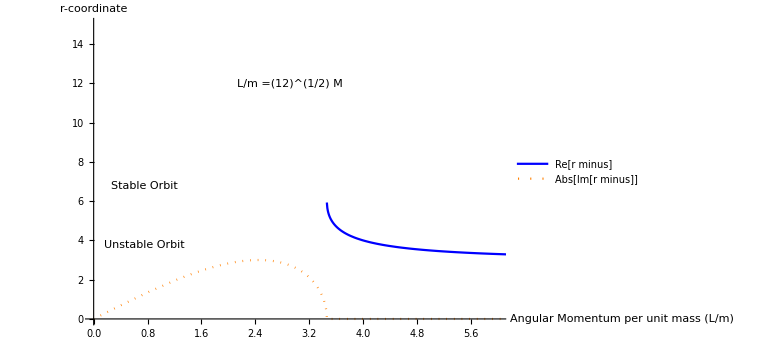

```mathematica
Plot[
{
rminus[l],Abs[Im[rminus[l]]]
},
{
l,0,20M
},
AxesLabel->{
"Angular Momentum per unit mass (L/m)","r-coordinate"
},
PlotLegends->{
"Re[r minus]","Abs[Im[r minus]]"
},
 ImageSize->Large,
Exclusions->None,
GridLines->{
{
{Sqrt[12]×M, Dashed}
},
{
{3M, {Pink, Dashed}}, {6M, {Red, Dashed}}
}
},
PlotStyle->{
{Blue,Thick},{Orange,Dotted}
},
PlotRange->{
{0,6M},{0,15M}
},
Epilog->plotCallouts
]
```

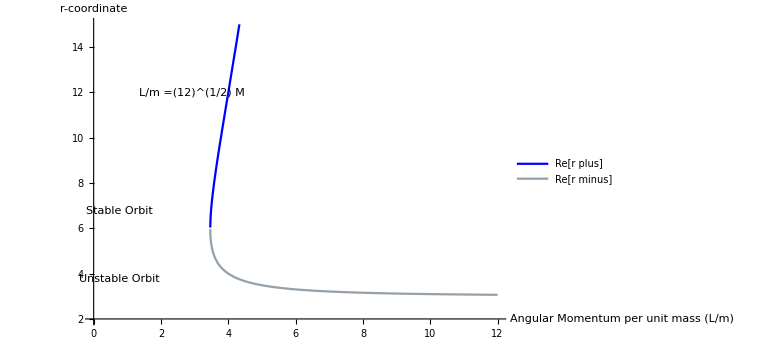

```mathematica
Plot[
{
rplus[l],rminus[l]
},
{
l,2,12M
},
AxesLabel->{
"Angular Momentum per unit mass (L/m)","r-coordinate"
},
PlotLegends->{
"Re[r plus]","Re[r minus]"
},
 ImageSize->Large,
Exclusions->None,
GridLines->{
{
{Sqrt[12]×M, Dashed}
},
{
{3M, {Pink, Dashed}}, {6M, {Red, Dashed}}
}
},
PlotStyle->{
{Blue},{Darker[LightBlue]}
},
PlotRange->{
{0,12M},{2,15M}
},
Epilog->plotCallouts
]
```